# GTDI

## Functions

## Auxiliaries

### Constants

```mathematica
scPermutationStream={{2,1},{3,2},{1,3},{3,1},{1,2},{2,3}};
scPermutationArm={{3,2},{1,3},{2,1},{2,3},{3,1},{1,2}};
```

```mathematica
scPermutationSignedStream=Flatten[Table[{j,i},{i,{1,-1}},{j,scPermutationStream}],1];
scPermutationSignedArm=Flatten[Table[{j,i},{i,{1,-1}},{j,scPermutationArm}],1];
```

```mathematica
numberMark1={"1","2","3","1'","2'","3'"};
numberMark2={"OverBar[1]","OverBar[2]","OverBar[3]","OverBar[1]'","OverBar[2]'","OverBar[3]'"};
```

```mathematica
polynomialSymbol={x,y,z,l,m,n};
```

### Rules

```mathematica
scPermutationToZeroRule=Thread[scPermutationStream->Table[0,{6}]];
scSignedPermutationToZeroRule=Thread[scPermutationSignedStream->Table[0,{12}]];
scSignedPermutationToEmptySetRule=Thread[scPermutationSignedStream->Table[{},{12}]];
```

```mathematica
scToStreamRule=Thread[scPermutationStream->(Subscript[η,#]&/@numberMark1)];
```

```mathematica
scToSignedStreamRule=Module[{stream=Subscript[η,#]&/@numberMark1},Thread[scPermutationSignedStream->Join[stream,-stream]]];
```

```mathematica
scToArmRule=Thread[scPermutationArm->numberMark1];
```

```mathematica
scToStreamDelayRule=Thread[scPermutationSignedArm->Join[numberMark1,numberMark2]];
```

```mathematica
streamDelayToPolynomialSymbolRule=Thread[Join[numberMark1,numberMark2]->Join[polynomialSymbol,1/polynomialSymbol]];
```

```mathematica
scToPolynomialSymbolRule=scToStreamDelayRule/.streamDelayToPolynomialSymbolRule;
```

```mathematica
polynomialSymbolSwitchRule=Thread[{l,m,n}->{x,y,z}];
```

### Auxiliary functions

```mathematica
toTrueSc[i_]:=Mod[i,3]+1;
```

```mathematica
pathToSc[path_List]:={toTrueSc/@path[[All,1]],Differences@path[[All,2]]};
```

```mathematica
pointSymmetrySwitch[{sc_,t_}]:={-sc,t};
scSymmetrySwitch[{a_Integer,b_}]:={a,b}/.{2->3,3->2};
scSymmetrySwitch[{a_List,b_}]:={a/.{2->3,3->2},b};
```

```mathematica
scToStream[sc_,dt_]:=Block[{sc1=Partition[sc,2,1],stream},stream=Table[If[dt[[i]]==-1,Reverse[sc1[[i]]],sc1[[i]]],{i,Length[dt]}];Transpose[{stream,-dt}]];
```

```mathematica
dtToDelayIndex[dt_]:=Block[{delayIndex=Prepend[Table[Range[i],{i,Length[dt]-1}],{}]},Table[AppendTo[delayIndex[[i]],i],{i,Flatten[Position[dt,1]]}];delayIndex];
```

```mathematica
scToStreamAndDelay[sc_,dt_]:=Block[{stream,delay,delayIndex,delays},stream=delay=scToStream[sc,dt];delayIndex=dtToDelayIndex[dt];delays=delay[[#]]&/@delayIndex;{stream,delays}];
```

```mathematica
pathToStreamAndDelay[path_List]:=scToStreamAndDelay@@pathToSc[path];
```

## Major functions

### Path conversion

```mathematica
pathJoin[{path1_,path2_}]/;path1[[-1]]==path2[[-1]]:=Join[path1,Rest@Reverse@path2];
```

```mathematica
pathPartition[path_]/;path[[1]]==path[[-1]]:=Block[{n},n=(Length[path]+1)/2;{path[[1;;n]],path[[-1;;-n;;-1]]}];
```

```mathematica
pathZero[{path1_,path2_}]:=Sort@Cases[Most@pathJoin[{path1,path2}],{_,0}]
```

```mathematica
pathZeroPosition[{path1_,path2_}]:=Union@Flatten[Position[Most@pathJoin[{path1,path2}],#]&/@pathZero[{path1,path2}]];
```

```mathematica
pathTransform["reverse"][{path1_,path2_}]:=Reverse[{path1,path2}];
```

```mathematica
pathTransform["scSymmetry"][{path1_,path2_}]:=pathTransform["reverse"]@Map[pointSymmetrySwitch,{path1,path2},{2}];
```

```mathematica
pathTransform["rotateLeft",n_][{path1_,path2_}]:=Block[{path,pn},path=Most@pathJoin[{path1,path2}];pn=Length[path1]-1;path=RotateLeft[path,n];path=Append[path,path[[1]]];pathPartition[path]];
```

```mathematica
pathTransform["initialPointAndDirection"][{path1_,path2_}]:=Block[{sc0,dsc,path},sc0=path1[[1,1]];path=Map[#-{sc0,0}&,{path1,path2},{2}];dsc=path1[[2,1]]-path1[[1,1]];If[dsc==1,path,Reverse@path]];
```

```mathematica
pathTransform["rotateLeftPath"][{path1_,path2_}]:=Block[{index,pathSet},index=(Rest@pathZeroPosition[{path1,path2}])-1;pathSet=Table[pathTransform["rotateLeft",i][{path1,path2}],{i,index}];pathTransform["initialPointAndDirection"]/@pathSet];
```

```mathematica
pathTransform["equivalentPath"][{path1_,path2_}]:=Block[{path={path1,path2},pathS,pathR,pathSR},pathS=pathTransform["scSymmetry"]@path;{pathR,pathSR}=pathTransform["rotateLeftPath"]/@{path,pathS};Join[{pathS},pathR,pathSR]];
```

```mathematica
pathTransform["IndexRotationPath"][{path1_,path2_}]:=Block[{path={path1,path2},pathSet},pathSet={path};AppendTo[pathSet,Map[#+{1,0}&,path,{2}]];AppendTo[pathSet,Map[#-{1,0}&,path,{2}]];pathSet];
```

```mathematica
pathTransform["neededEquivalentPath"][{path1_,path2_}]:=Block[{path={path1,path2},pathS1,pathS2},pathS1=pathTransform["scSymmetry"]@path;pathS2=pathTransform["rotateLeftPath"]@pathS1;If[MemberQ[Join[{pathS1},pathS2],path],pathTransform["IndexRotationPath"]@path,Flatten[pathTransform["IndexRotationPath"]/@{path,pathS1},1]]];
```

### TDI combination format

#### Laser link

```mathematica
pathToLaserLinkTrajectory[path_List]:=Block[{sc,dt},{sc,dt}=pathToSc[path];StringJoin@Riffle[ToString/@sc,If[#<0,"←","→"]&/@dt]];
pathToLaserLinkTrajectory[path1_List,path2_List]:=pathToLaserLinkTrajectory[Join[path1,Rest@Reverse[path2]]];
```

#### Defining formula

```mathematica
streamDelayToDelayOperator[delay_]:=If[Length[#]==0,1,Subscript["𝒟",StringJoin[#]]]&/@(delay/.scToStreamDelayRule);
```

```mathematica
pathToDelayOperatorFormula[path_List]:=Block[{stream,delay,stream1,delay1},{stream,delay}=pathToStreamAndDelay[path];stream1=stream/.scToSignedStreamRule;delay1=streamDelayToDelayOperator[delay];delay1.stream1];
pathToDelayOperatorFormula[path1_List,path2_List]:=pathToDelayOperatorFormula[path1]-pathToDelayOperatorFormula[path2];
```

#### Polynomial Vector

```mathematica
pathToPolynomialVector["m1g-TDI"][path_]:=Block[{stream,delay,v1},{stream,delay}=pathToStreamAndDelay[path];delay=Apply[Times,delay/.scToPolynomialSymbolRule,{1}];v1=scPermutationSignedStream/.Merge[Thread[stream->delay],Total]/.scSignedPermutationToZeroRule;v1[[1;;6]]-v1[[7;;12]]];
pathToPolynomialVector["m1g-TDI"][path1_,path2_]:=Subtract@@(pathToPolynomialVector["m1g-TDI"]/@{path1,path2});
```

```mathematica
pathToPolynomialVector["1g-TDI"][path_]:=pathToPolynomialVector["m1g-TDI"][path]/.polynomialSymbolSwitchRule;
pathToPolynomialVector["1g-TDI"][path1_,path2_]:=pathToPolynomialVector["m1g-TDI"][path1,path2]/.polynomialSymbolSwitchRule;
```

```mathematica
pathToPolynomialVector["0g-TDI"][path_]:=pathToPolynomialVector["1g-TDI"][path]/.{y->x,z->x};
pathToPolynomialVector["0g-TDI"][path1_,path2_]:=pathToPolynomialVector["1g-TDI"][path1,path2]/.{y->x,z->x};
```

### Sensitivity

#### Averaged response function (ARF)

```mathematica
aRF["f",1][u_]=4/3-2/u^2+Sin[2u]/u^3;
aRF["f",2][u_]=(-u*Cos[u]+Sin[u])/u^3-Cos[u]/3;
aRF["f",3][u_]=Log[4/3]-5/18+(-5Sin[u]+8Sin[2u]-3Sin[3u])/(8u)-(4+9Cos[u]+12Cos[2u]+Cos[3u])/(3*8u^2)+(-5Sin[u]+8Sin[2u]+5Sin[3u])/(3*8u^3)+CosIntegral[u]-2CosIntegral[2u]+CosIntegral[3u];
aRF["f",4][u_]=(-5Cos[u]+8Cos[2u]-3Cos[3u])/(8u)+(9Sin[u]+12Sin[2u]+Sin[3u])/(3*8u^2)-(8+5Cos[u]-8Cos[2u]-5Cos[3u])/(3*8u^3)-SinIntegral[u]+2SinIntegral[2u]-SinIntegral[3u];
aRF["f",5][u_]=-Log[4]+7/6+(11Sin[u]-4Sin[2u])/(4u)-(10+5Cos[u]-2Cos[2u])/(4u^2)+(5Sin[u]+4Sin[2u])/(4u^3)-2CosIntegral[u]+2CosIntegral[2u];
```

```mathematica
aRFVarRule1[vars_List]:=Thread[vars->Table[Exp[ⅈ*u],{Length@vars}]];
uReplaceRule=u->(2π*f*L)/c;
parameterReplaceRule["LISA"]={L->25*10^8,c->3*10^8,sa->3*10^(-15),sx->15*10^(-12)};
aRFSimplify[pF_]:=Refine[pF,u>0]//Simplify;
Attributes[aRFSimplify]={Listable};
```

```mathematica
polynomialVectorFourierTransform[pV_List]:=Block[{vars},vars=Union@@Variables/@pV;pV/.aRFVarRule1[vars]];
```

```mathematica
aRF["C",1][pF_List]:=Block[{value},value=Norm[#]^2&/@ComplexExpand[ExpToTrig@pF];aRFSimplify@Total@value];
aRF["C",2][pF_List]:=Block[{pFC,value1,value2,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{5,6,4}]];value=Table[2Re@ComplexExpand@ExpToTrig[value1[[i]]*value2[[i]]],{i,3}];aRFSimplify@Total@value];
aRF["C",3][pF_List]:=Block[{pFC,value1,value2,value3,value4,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{2,3,1}]];value3=pF[[{4,5,6}]];value4=pFC[[{6,4,5}]];
value=Table[2Re@ComplexExpand@ExpToTrig[(value1[[i]]*value2[[i]]+value3[[i]]*value4[[i]])*Exp[ⅈ*u]],{i,3}];aRFSimplify@Total@value];
aRF["C",4][pF_List]:=Block[{pFC,value1,value2,value3,value4,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{2,3,1}]];value3=pF[[{4,5,6}]];value4=pFC[[{6,4,5}]];
value=Table[2Im@ComplexExpand@ExpToTrig[(value1[[i]]*value2[[i]]+value3[[i]]*value4[[i]])*Exp[ⅈ*u]],{i,3}];aRFSimplify@Total@value];
aRF["C",5][pF_List]:=Block[{pFC,value1,value2,value3,value},pFC=pF/.{Exp[xx_]:>Exp[-xx]};value1=pF[[{1,2,3}]];value2=pFC[[{4,5,6}]];value3=pFC[[{6,4,5}]];
value=Table[2Re@ComplexExpand@ExpToTrig[value1[[i]]*value2[[i]]+value1[[i]]*value3[[i]]],{i,3}];aRFSimplify@Total@value];
```

```mathematica
polynomialVectorToARF[pv_]:=Block[{pF,constant,cValue,fValue},pF=polynomialVectorFourierTransform[pv];constant={1/2,1,3/4,-3/4,1/4};cValue=Table[aRF["C",i][pF],{i,5}];fValue=Table[aRF["f",i][u],{i,5}];(constant*cValue).fValue//TrigReduce//Simplify];
```

```mathematica
pathToARF[path_List]:=polynomialVectorToARF@(pathToPolynomialVector["1g-TDI"]@@path);
```

#### Noise PSD

```mathematica
polynomialVectorToNoisePSD[pv_]:=Block[{pF,constant,cValue,fValue,c1,c2,n1,n2},pF=polynomialVectorFourierTransform[pv];constant={1,2};cValue=Table[aRF["C",i][pF],{i,2}];c1=(1+((4*10^-4*2π L)/(u c))^2)(1+((u c)/(2π L*8*10^-3))^4);c2=(1+((2*10^-3*2π L)/(u c))^4);n1=(2L^2*sa^2*c1)/(u^2*c^4)+(u^2*sx^2*c2)/L^2;n2=(L^2*sa^2*c1)/(u^2*c^4)Cos[u];(constant*cValue).{n1,n2}//TrigReduce//Simplify];
```

```mathematica
pathToNoisePSD[path_List]:=polynomialVectorToNoisePSD@(pathToPolynomialVector["1g-TDI"]@@path);
```

#### Sensitivity function

```mathematica
polynomialVectorToSensitivityFunction[pv_]:=Block[{arf,noisePSD},arf=polynomialVectorToARF@pv;noisePSD=polynomialVectorToNoisePSD@pv;Sqrt[(5noisePSD)/(2arf)]];
```

```mathematica
pathToSensitivityFunction[path_]:=polynomialVectorToSensitivityFunction@(pathToPolynomialVector["1g-TDI"]@@path);
```

```mathematica
pathToSFValue[path_,freq_]:=(pathToSensitivityFunction@path)/.uReplaceRule/.parameterReplaceRule["LISA"]/.{f->freq}//N
```

### Plot

#### Space-time diagram

```mathematica
spaceTimePlot2[{path1_List,path2_List},opts___]:=Block[{n1=Length[path1],n2=Length[path2],path1A={-1,1}*#&/@path1,path2A={-1,1}*#&/@path2,scColor={Gray,Magenta,Darker@Green},scRange,tRange,pLine1,pLine2,pLinePath1,pLinePath2,radius,pPoint,pXAxis,pYAxis,pAxisLable},{scRange,tRange}=MinMax/@Join@@@Transpose[CoordinateBounds/@{path1A,path2A}];pLine1={GrayLevel[0.7],Dashed,Thin,Line[Table[{{scRange[[1]],i},{scRange[[2]],i}},{i,tRange[[1]],tRange[[2]]}]]};pLine2=Table[{scColor[[toTrueSc[-i]]],Dashed,Line[{{i,tRange[[1]]},{i,tRange[[2]]}}]},{i,scRange[[1]],scRange[[2]]}];
pLinePath1={Red,Thick,Line[#+{0,0.02}&/@path1A]};
pLinePath2={Darker@Blue,Thick,Dashed,Line[#-{0,0.02}&/@path2A]};radius=0.005*(Differences[scRange][[1]]+Differences[tRange][[1]]);pPoint={FaceForm[Black],Disk[path1A[[1]],radius],Rectangle[path1A[[-1]]+{-1,-1}*radius,path1A[[-1]]+{1,1}*radius]};pXAxis=Table[Text[toTrueSc[-i],{i,tRange[[1]]-0.12}],{i,scRange[[1]],scRange[[2]]}];pYAxis=Table[Text[i,{scRange[[1]]-0.12,i}],{i,tRange[[1]],tRange[[2]]}];pAxisLable={Black,Text[Row[{Style["SC ",FontFamily->"Times New Roman",FontSize->12],Style["i",FontFamily->"Times",FontSize->12,Italic]}],{Mean[scRange],tRange[[1]]-0.25}],Text[Row[{Style["time unit ( ",FontFamily->"Times New Roman",FontSize->12],Style["t / T",FontFamily->"Times",FontSize->12,Italic],Style[" )",FontFamily->"Times New Roman",FontSize->12]}],{scRange[[1]]-0.3,Mean[tRange]},{0,0},{0,1}]};Graphics[{pLine1,pLine2,pLinePath1,pLinePath2,pPoint,pXAxis,pYAxis,pAxisLable},opts]]
```

#### Sensitivity function diagram

```mathematica
sensitivityFunctionPlot["SF"][sf_,opts___]:=LogLogPlot[Evaluate[sf/.uReplaceRule/.parameterReplaceRule["LISA"]],{f,10^-4,1},opts,PlotRange->{Automatic,{10^-20,10^-15}},WorkingPrecision->20,Frame->True,GridLines->Automatic,AspectRatio->1,Exclusions->None]
```

```mathematica
sensitivityFunctionPlot["PV"][pv_,opts___]:=sensitivityFunctionPlot["SF"][polynomialVectorToSensitivityFunction@pv,opts]/;ArrayDepth[pv]==1;
sensitivityFunctionPlot["PV"][pv_,opts___]:=sensitivityFunctionPlot["SF"][polynomialVectorToSensitivityFunction/@pv,opts]/;ArrayDepth[pv]==2;
```

```mathematica
sensitivityFunctionPlot["path"][path_,opts___]:=sensitivityFunctionPlot["SF"][pathToSensitivityFunction@path,opts]/;Depth[path]==4;
sensitivityFunctionPlot["path"][path_,opts___]:=sensitivityFunctionPlot["SF"][pathToSensitivityFunction/@path,opts]/;Depth[path]==5;
```

## Usage

Run all codes in “Functions” before running the following codes

Place the folder “data ” in the folder where the current file is located

## Example 1

Import GTDI data

```mathematica
data[16,"2g-TDI"]=Import[NotebookDirectory[]<>"data\\16-2g-TDI.wdx"];
data[16,"2g-TDI-SF"]=Import[NotebookDirectory[]<>"data\\16-2g-TDI-SF.wdx"];
data[16,"m2g-TDI"]=Import[NotebookDirectory[]<>"data\\16-m2g-TDI.wdx"];
```

```mathematica
Length/@{data[16,"2g-TDI"],data[16,"m2g-TDI"]}
```

{38,9}

Plot space-time diagram

{{{0,0},{1,-1},{0,-2},{-1,-3},{-2,-2},{-3,-3},{-2,-4},{-1,-5},{0,-4}},{{0,0},{-1,-1},{-2,0},{-3,-1},{-2,-2},{-1,-3},{0,-2},{1,-3},{0,-4}}}

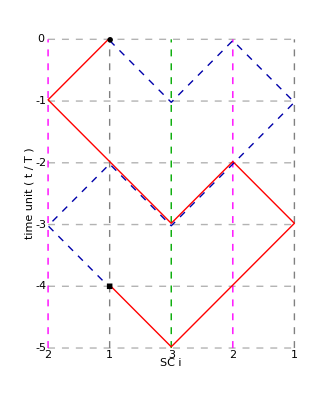

```mathematica
pa1=data[16,"2g-TDI"][[2]]
spaceTimePlot2@pa1
```

other formats of the TDI combination

```mathematica
pathToLaserLinkTrajectory@@pa1
pathToDelayOperatorFormula@@pa1//Simplify
pathToPolynomialVector["m1g-TDI"]@@pa1
```

1←2←1←3→2←1←2←3→1→2→1←3→2→1→2←3→1

-((-1+𝒟_(2'OverBar[1]3')+𝒟_(2'OverBar[1]3'31OverBar[2]')-𝒟_(33'2'OverBar[1]3')) η_1)+(-1+𝒟_(2'OverBar[1]3'31OverBar[2]')+𝒟_(33')-𝒟_(33'2'OverBar[1]3'31OverBar[2]')) η_(1')+𝒟_(2'OverBar[1]) η_2-𝒟_(2'OverBar[1]3'3) η_2-𝒟_(33'2'OverBar[1]) η_2+𝒟_(33'2'OverBar[1]3'3) η_2-𝒟_(2'OverBar[1]) η_(2')-𝒟_(2'OverBar[1]3'31OverBar[2]'3) η_(2')+𝒟_3 η_(2')+𝒟_(33'2'OverBar[1]) η_(2')

{1-(m n)/x-n z+(m n^2 z)/x,m/x-(2 m n z)/x+(m n^2 z^2)/x,0,-1+2 n z-n^2 z^2,-m/x+z+(m n z)/x-n z^2,0}

some equivalent TDI combinations of the TDI combination

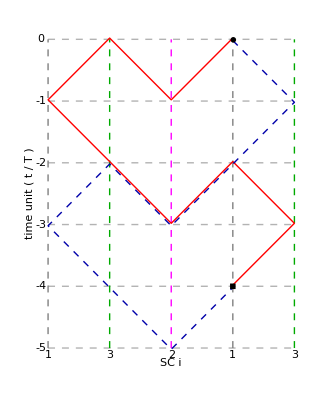
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
pa1b=pathTransform["equivalentPath"]@pa1;
spaceTimePlot2/@pa1b
```

Plot sensitivity function

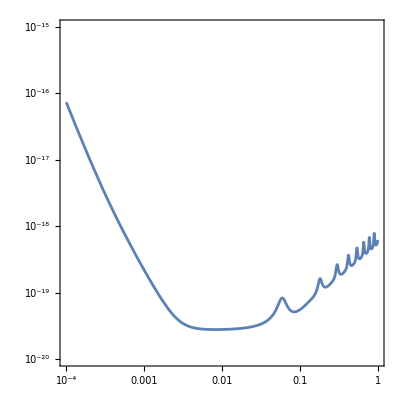

```mathematica
sensitivityFunctionPlot["path"]@pa1
```

The second-generation TDI combinations with 16-link has 11 different sensitivity curves

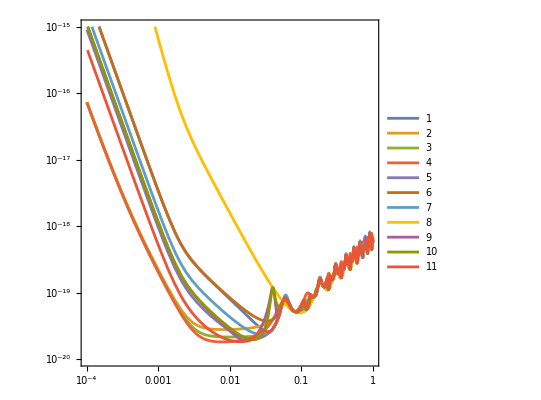

```mathematica
sensitivityFunctionPlot["path"][data[16,"2g-TDI-SF"],PlotLegends->Range[11]]
```

## Example 2

Import GTDI data

```mathematica
data[30,"m3g-TDI"]=Import[NotebookDirectory[]<>"data\\30-m3g-TDI.wdx"];
Length@data[30,"m3g-TDI"]
```

452

Plot space-time diagram

{{{0,0},{1,-1},{0,-2},{-1,-1},{-2,-2},{-3,-3},{-4,-4},{-3,-5},{-2,-6},{-3,-7},{-2,-8},{-1,-9},{0,-10},{1,-9},{0,-8},{-1,-9}},{{0,0},{-1,-1},{-2,-2},{-3,-3},{-4,-2},{-3,-1},{-2,-2},{-3,-3},{-2,-4},{-3,-5},{-4,-6},{-3,-7},{-4,-8},{-3,-9},{-2,-8},{-1,-9}}}

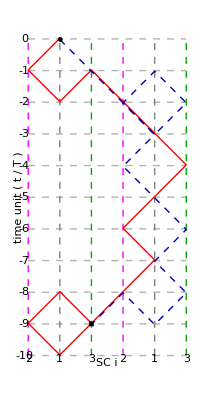

```mathematica
pa2=data[30,"m3g-TDI"][[1]]
spaceTimePlot2@pa2
```

other formats of the TDI combination

```mathematica
pathToLaserLinkTrajectory@@pa2
pathToDelayOperatorFormula@@pa2//Simplify
pathToPolynomialVector["m1g-TDI"]@@pa2
```

1←2←1→3←2←1←3←1←2←1←2←3←1→2→1←3→2←1→3→1→3→1→2→1→2→1←3←1→2→3→1

-((-1+𝒟_(2'1'3'OverBar[2]OverBar[2]')+𝒟_(2'1'3'OverBar[2]OverBar[2]'33')-𝒟_(33'OverBar[2]1'3'2'2)-𝒟_(33'OverBar[2]1'3'2'233')+𝒟_(33'OverBar[2]1'3'2'233'312OverBar[3]'OverBar[3])) η_1)+(-1+𝒟_(2'1'3'OverBar[2]OverBar[2]')-𝒟_(2'1'3'OverBar[2]OverBar[2]'33'33')-𝒟_(2'1'3'OverBar[2]OverBar[2]'33'33'2'2)+𝒟_(33'OverBar[2]1'3')+𝒟_(33'OverBar[2]1'3'2'233'312OverBar[3]'OverBar[3])) η_(1')-𝒟_(2'1'3'OverBar[2]OverBar[2]'33'33'2'22'2OverBar[3]') η_2+𝒟_(33'OverBar[2]1'3'2'233'3) η_2-𝒟_(2'1') η_(2')-𝒟_(2'1'3'OverBar[2]OverBar[2]'3) η_(2')-𝒟_(2'1'3'OverBar[2]OverBar[2]'33'3) η_(2')+𝒟_(2'1'3'OverBar[2]OverBar[2]'33'33'2'22'2OverBar[3]') η_(2')+𝒟_3 η_(2')+𝒟_(33'OverBar[2]1') η_(2')+𝒟_(33'OverBar[2]1'3'2'23) η_(2')-𝒟_(33'OverBar[2]1'3'2'233'312OverBar[3]') η_(2')+𝒟_(2'1'3'OverBar[2]) η_3-𝒟_(2'1'3'OverBar[2]OverBar[2]'33'33'2') η_3-𝒟_(2'1'3'OverBar[2]OverBar[2]'33'33'2'22') η_3-𝒟_(33'OverBar[2]) η_3+𝒟_(33'OverBar[2]1'3'2') η_3+𝒟_(33'OverBar[2]1'3'2'233'31) η_3-𝒟_(2') η_(3')+𝒟_(33'OverBar[2]) η_(3')

{1-(l n)/y+l m n^2 z-(l n^2 z)/y+l m n^3 z^2-l m n^2 x y z^2,-l m^2 n^2 y z^2+l m n^3 z^3,(l m n)/y-(n z)/y+(l m n^2 z)/y-l m^2 n^3 z^2-(l m n^3 z^2)/y+l m n^3 x z^3,-1+(l n)/y+(l n^2 z)/y-l m n^3 z^2-(l n^3 z^2)/y+l m n^2 x y z^2,-l m+z+l m n^2 z^2-(l n^2 z^2)/y+l m^2 n^2 y z^2-l m n^2 x y z^3,-m+(n z)/y}

Plot sensitivity function

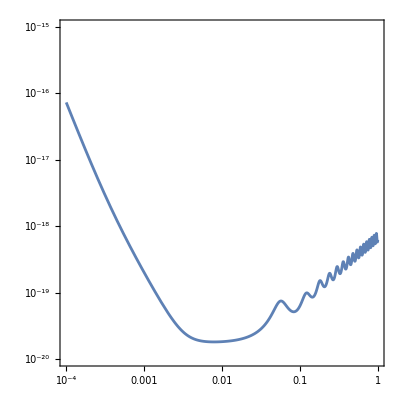

```mathematica
sensitivityFunctionPlot["path"]@pa2
```